```mathematica
Quit
```

```mathematica
(* Mock Data *)
```

```mathematica
SetDirectory[NotebookDirectory[]];
Needs["ErrorBarPlots`"];
```

```mathematica
(* Some mock data *)
SeedRandom[12348551];
model[x_,a_,b_,c_]:=a+(x-b) Exp[-c x^2]
σ=0.03;
data=Table[{x,model[x,1/4,1/4,1/2]+RandomVariate[NormalDistribution[0,σ]],RandomVariate[NormalDistribution[σ,σ/5]]},{x,0.025,1.55,0.05}];ndat=Length[data];
```

```mathematica
(* Definitions *)
chi2GA[f_,dat_]:=Module[{temp,ft},ft=(f/.x->#)&;temp=Sum[((dat[[ii,2]]-(ft[dat[[ii,1]]]))/dat[[ii,3]])^2,{ii,1,Length[dat]}]];
chi2model[a_,b_,c_]:=Sum[((data[[ii,2]]-model[data[[ii,1]],a,b,c])/data[[ii,3]])^2,{ii,1,Length[data]}];
```

χ^2/dof= 1.02588

Number of points = 31

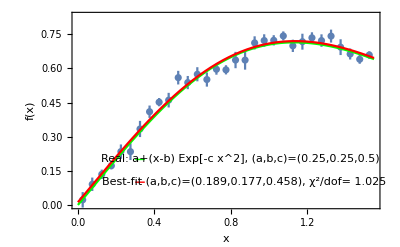

```mathematica
(* Best fit // normal case *)
fmin=FindMinimum[chi2model[a,b,c],{a,0.2},{b,.5},{c,0.5}];
Print["χ^2/dof= ",fmin[[1]]/ndat]
Print["Number of points = ",ndat]
(* Plots of the mock data *)
err=ErrorListPlot[data,PlotRange->{{0,1.55},{0,.83}}];
pl0=Plot[{model[x,1/4,1/4,1/2],model[x,a,b,c]/.fmin[[2]]},{x,0,1.55},PlotStyle->{Green,Red}];
Show[err,pl0,Graphics[{{Green,Line[{{.3,.2},{.35,.2}}]},{Red,Line[{{.3,.1},{.35,.1}}]}}],Frame->True,Axes->False,Epilog->{Text["Real: a+(x-b) Exp[-c x^2], (a,b,c)=(0.25,0.25,0.5)",{.85,.2}],Text["Best-fit (a,b,c)=(0.189,0.177,0.458), χ^2/dof= 1.025",{.87,.1}]},FrameLabel->{"x","f(x)"}]
```

```mathematica
(* end *)
```

```mathematica
(* GA theory *)
```

```mathematica
poly[x_]:=x
polyxtox[x_]:=x^x
(* grammar={poly,Exp,Sin,Cos,Tan,Log};*)
grammar={poly,polyxtox};
(* Expression length *)
length=4;
depth=4;
rang1={-1,1};
rang2={1,Length[grammar]};
rang3={0,2};
rang4={0,9};
toursize=4;
selectionrate=0.3;
```

```mathematica
func[x_,kid_,gram_]:=Sum[kid[[i,1]] (gram[[kid[[i,2]]]]@(kid[[i,3]]x))^kid[[i,4]],{i,1,length}]
mutation[kid_]:=Module[{mut,rep},
rep={RandomInteger[{1,length}],RandomInteger[{1,depth}]};
mut=Which[rep[[2]]==1,RandomReal[rang1],rep[[2]]==2,RandomInteger[rang2],rep[[2]]==3,RandomReal[rang3],rep[[2]]==4,RandomInteger[rang4]];
ReplacePart[kid,rep->mut]]
cross[{kid1_,kid2_}]:=Module[{len},len=RandomInteger[{1,length-1}];
{Join[kid1[[1;;len]],kid2[[(len+1);;-1]]],Join[kid1[[(len+1);;-1]],kid2[[1;;len]]]}]
```

```mathematica
tournament[fit_,tours_]:=Sort[RandomSample[fit,tours],#1[[1]]>#2[[1]]&][[1,2]]
negativetournament[fit_,tours_]:=Sort[RandomSample[fit,tours],#1[[1]]>#2[[1]]&][[-1,2]]
```

```mathematica
GAevo[randomseed_,maxgens_,pop_,crossrate_,mutrate_,verbose_]:=Module[{prog,bestfitperstep,chromosomes,t1,pigs,fitness,p1,p2,maxchilds},
maxchilds=Round[selectionrate*pop,2];
SeedRandom[randomseed];
ParallelEvaluate[SeedRandom[randomseed]];
bestfitperstep={};
chromosomes=ParallelTable[{RandomReal[rang1],RandomInteger[rang2],RandomReal[rang3],RandomInteger[rang4]},{pop},{length}];
t1=AbsoluteTime[];
Do[pigs=(x+x^2*(1+func[x,#,grammar]))&/@chromosomes;
fitness=Sort[ParallelTable[{-MemoryConstrained[TimeConstrained[chi2GA[pigs[[j]],data],.5],10^7],j},{j,1,Length[pigs]}],#1[[1]]>#2[[1]]&];AppendTo[bestfitperstep,{fitness[[1,1]],pigs[[fitness[[1,2]]]],chromosomes[[fitness[[1,2]]]]}];p1=Partition[RandomSample[Table[negativetournament[fitness,toursize],{10maxchilds}]//Union,maxchilds],2];p2=Partition[RandomSample[Table[tournament[fitness,toursize],{10maxchilds}]//Union,maxchilds],2];Do[{chromosomes[[p1[[jj,1]]]],chromosomes[[p1[[jj,2]]]]}=If[RandomReal[{0,1}]<crossrate,
cross[{chromosomes[[p2[[jj,1]]]], chromosomes[[p2[[jj,2]]]]}],{chromosomes[[p1[[jj,1]]]],chromosomes[[p1[[jj,2]]]]}];,{jj,1,Length[p1]}];Do[{chromosomes[[p1[[jj,1]]]],chromosomes[[p1[[jj,2]]]]}=If[RandomReal[{0,1}]<mutrate,
{mutation[chromosomes[[p2[[jj,1]]]]],mutation[chromosomes[[p2[[jj,2]]]]]},{chromosomes[[p1[[jj,1]]]],chromosomes[[p1[[jj,2]]]]}];,{jj,1,Length[p1]}];
prog`int++,{maxgens}];
If[verbose==True,
Print["Time taken: ",AbsoluteTime[]-t1," sec"];
Print["χ_min^2 = ",Abs[fitness[[1,1]]]];
Print["Best-fit function is: "];
Print[bestfitperstep[[-1,2]]];
Speak["The end"];];
bestfitperstep]
```

```mathematica
(* end *)
```

```mathematica
(* GA // one fit *)
```

```mathematica
LaunchKernels[7];
```

```mathematica
(* Run the GA code with 1 random seed *)
generations=1500;
prog`int=0;
ProgressIndicator[Dynamic[prog`int],{0,generations}]
(* {randomseed, maxgens, population, crossoverrate, mutationrate, verbose (True/False)} *)
GApop=GAevo[1234,generations,100,0.75,0.3,True];
```

Time taken: 125.8198 sec

χ_min^2 = 29.176

Best-fit function is:

x+x^2 (-0.512897+1.55289 0.0891856^(0.80267 x) x^(0.80267 x))

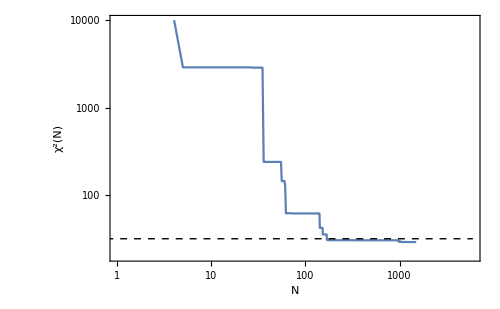

```mathematica
(* Plot of the generations *)
ListLogLogPlot[GApop[[All,1]]//Abs,Joined->True,PlotRange->{{1,4 generations},{20,10^4}},Frame->True,FrameStyle->Black,Epilog->{{Dashed,Line[{{0.1,fmin[[1]]},{4generations,fmin[[1]]}}//Log]},Inset[ListLogLogPlot[GApop[[All,1]]//Abs,Joined->True,PlotRange->{{100,1500},{28,34}},Frame->True,FrameStyle->Black,Epilog->{Dashed,Line[{{0.1,fmin[[1]]},{4generations,fmin[[1]]}}//Log]},FrameLabel->{"N","χ^2(N)"},FrameStyle->Black,BaseStyle->FontSize->14,ImageSize->250],Scaled[{0.7,0.65}]]},FrameLabel->{"N","χ^2(N)"},FrameStyle->Black,BaseStyle->FontSize->14,ImageSize->500]
```

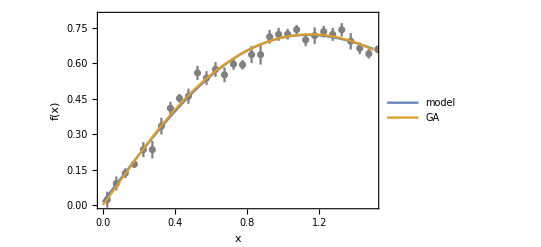

```mathematica
(* Plot of the best-fit real model vs the best-fit GA *)
plr={{0,1.5},{0,.8}};
Show[ErrorListPlot[data,PlotRange->plr,PlotStyle->Gray],Plot[{model[x,a,b,c]/.fmin[[2]],GApop[[-1,2]]}//Evaluate,{x,0,1.5},PlotRange->plr,Frame->True,PlotLegends->{"model","GA"}],Frame->True,Axes->False,FrameLabel->{"x","f(x)"},FrameStyle->Black,BaseStyle->FontSize->15,PlotRange->plr]
```

```mathematica
(* The GA best-fit *)
GApop[[-1,2]]
```

x+x^2 (-0.512897+1.55289 0.0891856^(0.80267 x) x^(0.80267 x))

```mathematica
fGA[x_]:=x+x^2 (-0.5128968007741621+1.5528875590678615 0.08918560377688678^(0.802670433991981 x) x^(0.802670433991981 x))
```

```mathematica
(* Compare the chi^2 *)
chi2GA[model[x,a,b,c]/.fmin[[2]],data]
chi2GA[fGA[x],data]
```

31.8024

29.176

```mathematica
(* Error analysis doing the path integral *)
df[x_,a1_,a2_,a3_]:=x(a1+a2 x+a3 x^2)
chi2CI[a1_?NumericQ,a2_?NumericQ,a3_?NumericQ]:=Module[{CI},CI=Table[1/2 (Erf[1/(√2 data[[i,3]])(df[data[[i,1]],a1,a2,a3]+fGA[data[[i,1]]]-data[[i,2]])]+Erf[1/(√2 data[[i,3]])(df[data[[i,1]],a1,a2,a3]-fGA[data[[i,1]]]+data[[i,2]])]),{i,1,Length[data]}];
Sum[(CI[[i]]-Erf[1/(√2)])^2,{i,1,Length[data]}]]
chi2GApluserr[a1_?NumericQ,a2_?NumericQ,a3_?NumericQ]:=chi2GA[fGA[x]+df[x,a1,a2,a3],data]
chi2tot[a1_,a2_,a3_]:=chi2CI[a1,a2,a3]+chi2GApluserr[a1,a2,a3]
```

```mathematica
fminerr2=FindMinimum[chi2tot[a1,a2,0],{a1,0.11,0.111},{a2,0.11,0.111},MaxIterations->500]
fminerr3=FindMinimum[chi2tot[a1,a2,a3],{a1,0.11,0.111},{a2,0.11,0.111},{a3,0.11,0.111},MaxIterations->500]
```

{41.2274,{a1→0.0142702,a2→-0.00660607}}

{41.121,{a1→0.0270786,a2→-0.0333045,a3→0.0125076}}

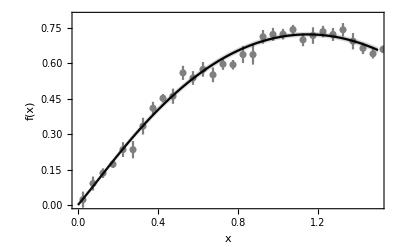

```mathematica
(* Final plot with errors *)
ϵ0={-1,0,1};
col=GrayLevel[0.3,0.2];
plot=Show[ErrorListPlot[data,PlotRange->plr,PlotStyle->Gray],Plot[fGA[x]+ϵ0 df[x,a1,a2,a3]/.fminerr3[[2]]//Evaluate,{x,0,1.5},PlotRange->plr,Frame->True,PlotStyle->{col,Black,col},Filling->{1->{{3},col}}],Frame->True,Axes->False,FrameLabel->{"x","f(x)"},FrameStyle->Black,BaseStyle->FontSize->15,PlotRange->plr]
```

```mathematica
Export["plot_case_1.pdf",plot,ImageSize->500]
```

```mathematica
(* end *)
```

```mathematica
(* GA // multiple fits *)
```

```mathematica
LaunchKernels[7];
```

```mathematica
(* Run the GA with multiple random seeds // change the sample parameter *)
```

```mathematica
Clear[prog`int,prog`pop,GApop];
generations=300;
samples=4;
prog`int=0;
prog`pop=0;
ProgressIndicator[Dynamic[prog`int],{0,generations}]
ProgressIndicator[Dynamic[prog`pop],{0,samples}]
(* {randomseed, maxgens, population, crossoverrate, mutationrate, verbose (True/False)} *)
Do[GApop[jj]=GAevo[1234jj,generations,100,0.75,0.3,False];prog`pop++;prog`int=0;,{jj,1,samples}];
```

```mathematica
Export["test_samples"<>".zip",{"test_samples"<>".m"->Table[GApop[jj],{jj,1,samples}]}]
```

```mathematica
(* Plot the chi^2 as a function of the generations *)
```

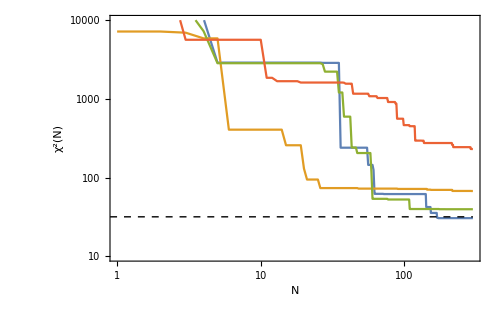

```mathematica
ListLogLogPlot[Table[GApop[jj][[All,1]]//Abs,{jj,1,samples}],Joined->True,PlotRange->{{1, generations},{10,10^4}},Frame->True,FrameStyle->Black,Epilog->{{Dashed,Line[{{0.1,fmin[[1]]},{generations,fmin[[1]]}}//Log]}},FrameLabel->{"N","χ^2(N)"},FrameStyle->Black,BaseStyle->FontSize->14,ImageSize->500]
```

```mathematica
(* The best-fitting GA functions *)
GAfuncs=Table[GApop[i][[-1,2]],{i,1,samples}];
```

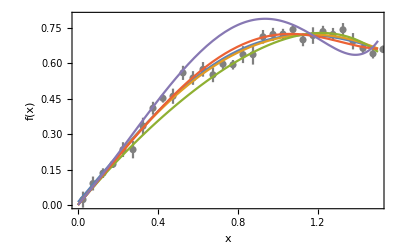

```mathematica
(* Plot of the best-fit real model vs the best-fit GA *)
plr={{0,1.5},{0,.8}};
Show[ErrorListPlot[data,PlotRange->plr,PlotStyle->Gray],Plot[{model[x,a,b,c]/.fmin[[2]],GAfuncs}//Evaluate,{x,0,1.5},PlotRange->plr,Frame->True],Frame->True,Axes->False,FrameLabel->{"x","f(x)"},FrameStyle->Black,BaseStyle->FontSize->15,PlotRange->plr]
```

```mathematica
bestGA=Table[{chi2GA[GAfuncs[[i]],data],i},{i,1,samples}]//Sort
```

{{30.6024,1},{39.6982,3},{67.6405,2},{230.958,4}}

```mathematica
GAfuncs[[bestGA[[1,2]]]]
```

x+x^2 (-0.509202+1.13788 0.0693385^(0.624047 x) x^(0.624047 x))

```mathematica
fGA[x_]:=x+x^2 (-0.5092015229139539+1.1378791073169827 0.0693385029774447^(0.6240465267970023 x) x^(0.6240465267970023 x))
```

```mathematica
chi2GA[model[x,a,b,c]/.fmin[[2]],data]
chi2GA[fGA[x],data]
```

31.8024

30.6024

```mathematica
(* Error analysis doing the path integral *)
df[x_,a1_,a2_,a3_]:=x(a1+a2 x+a3 x^2)
chi2CI[a1_?NumericQ,a2_?NumericQ,a3_?NumericQ]:=Module[{CI},CI=Table[1/2 (Erf[1/(√2 data[[i,3]])(df[data[[i,1]],a1,a2,a3]+fGA[data[[i,1]]]-data[[i,2]])]+Erf[1/(√2 data[[i,3]])(df[data[[i,1]],a1,a2,a3]-fGA[data[[i,1]]]+data[[i,2]])]),{i,1,Length[data]}];
Sum[(CI[[i]]-Erf[1/(√2)])^2,{i,1,Length[data]}]]
chi2GApluserr[a1_?NumericQ,a2_?NumericQ,a3_?NumericQ]:=chi2GA[fGA[x]+df[x,a1,a2,a3],data]
chi2tot[a1_,a2_,a3_]:=chi2CI[a1,a2,a3]+chi2GApluserr[a1,a2,a3]
```

```mathematica
fminerr2=FindMinimum[chi2tot[a1,a2,0],{a1,0.11,0.111},{a2,0.11,0.111},MaxIterations->500]
fminerr3=FindMinimum[chi2tot[a1,a2,a3],{a1,0.11,0.111},{a2,0.11,0.111},{a3,0.11,0.111},MaxIterations->500]
```

{39.4231,{a1→0.0362194,a2→-0.0237727}}

{39.0612,{a1→0.059936,a2→-0.0729729,a3→0.0229331}}

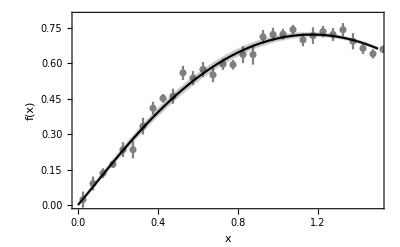

```mathematica
(* Final plot with errors *)
ϵ0={-1,0,1};
col=GrayLevel[0.3,0.2];
plot=Show[ErrorListPlot[data,PlotRange->plr,PlotStyle->Gray],Plot[fGA[x]+ϵ0 df[x,a1,a2,a3]/.fminerr3[[2]]//Evaluate,{x,0,1.5},PlotRange->plr,Frame->True,PlotStyle->{col,Black,col},Filling->{1->{{3},col}}],Frame->True,Axes->False,FrameLabel->{"x","f(x)"},FrameStyle->Black,BaseStyle->FontSize->15,PlotRange->plr]
```

```mathematica
Export["plot.pdf",plot,ImageSize->500]
```

```mathematica
(* end *)
```